```mathematica
m=ZetaFunction[WheelGraph[6]]
```

SparseArray[…]

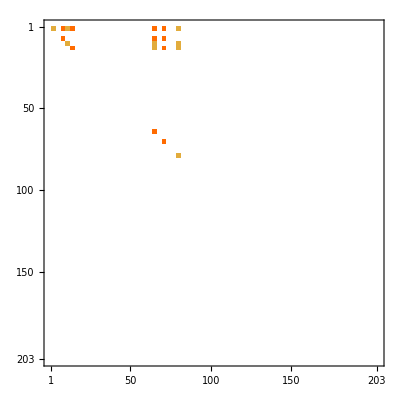

```mathematica
MatrixPlot[m]
```

```mathematica
FixDiagonal[m_]:=Table[If[i==j,1,m[[i,j]]],{i,Length[m]},{j,Length[m]}]
```

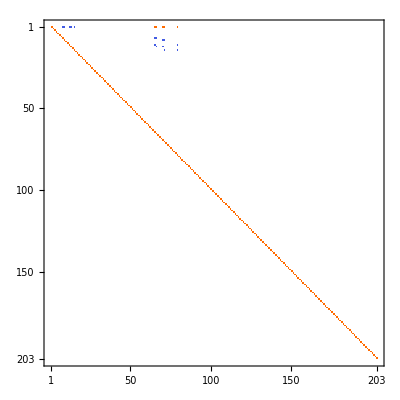

```mathematica
FixDiagonal[m]//Inverse//MatrixPlot
```

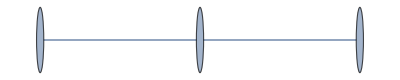

```mathematica
g=Graph[{1<->2,2<->3}]
```

```mathematica
FindFullFormula[g]
```

{v1x2x3,v13x2}

```mathematica
h3=Table[SymbolToLabel[allGraphs3[k,"colofour"]],{k,allGraphs3AtomKeys}]
```

{1♁2♁3,1♁23,13♁2,12♁3,123}

```mathematica
MatrixForm[ZetaFunction[g],TableHeadings->{h3, Map[Rotate[#,Pi/2]&,h3]}]
```

( | 1♁2♁3 | 1♁23 | 13♁2 | 12♁3 | 123
1♁2♁3 | 1 | 0 | 1 | 0 | 0
1♁23 | 0 | 0 | 0 | 0 | 0
13♁2 | 0 | 0 | 1 | 0 | 0
12♁3 | 0 | 0 | 0 | 0 | 0
123 | 0 | 0 | 0 | 0 | 0)

```mathematica
h=EdgeAdd[g,1<->3]
```

-Graphics-

```mathematica
ZetaFunction[h]//Normal//Inverse
```

Inverse[{{1,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}]

```mathematica
CalculateInOutFormulaMany[g]//Expand
```

a1-a1 b2-a1 c3+a1 b2 c3

```mathematica
CalculateInOutFormulaMany[h]//Expand
```

2 a1-2 a1 b2-a1 c3+a1 b2 c3

```mathematica
Table[allGraphs3[k,"colofour"],{k,allGraphs3AtomKeys}]
```

{v1x2x3,v1x23,v13x2,v12x3,v123}

```mathematica
MatrixForm[ZetaFunction[h],TableHeadings->{h3, Map[Rotate[#,Pi/2]&,h3]}]
```

( | 1♁2♁3 | 1♁23 | 13♁2 | 12♁3 | 123
1♁2♁3 | 1 | 0 | 0 | 0 | 0
1♁23 | 0 | 0 | 0 | 0 | 0
13♁2 | 0 | 0 | 0 | 0 | 0
12♁3 | 0 | 0 | 0 | 0 | 0
123 | 0 | 0 | 0 | 0 | 0)

```mathematica
ZetaFunction[EdgeContract[h,1<->3]]//MatrixForm
```

(1 | 0
0 | 0)